```mathematica
f[x1_,x2_]=-12x1-7.5x2-5; (*функція*)
g[x1_,x2_]={2-2 x1^2-x2^2,x1+x2-1.5,x1,x2}; (* область пошуку *)
ϵ=10.^-3;
h[x1_,x2_]={x1+0,1-x1,x2+0.5,1.5-x2};  (* загальна область *)
```

Область пошуку

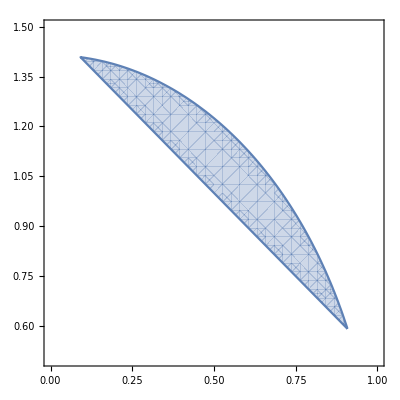

```mathematica
Print["Область пошуку"]
RegionPlot[2-2 x1^2-x2^2≥0&&x1+x2-1.5≥0&&x1≥0&&x2≥0,{x1,0,1},{x2,0.5,1.5}]
```

NMinimize::incst: NMinimize was unable to generate any initial points satisfying the inequality constraints {1.5-x1-x2≤0,-2+2 x1^2+x2^2≤0}. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

Таблиця результатів:

k | x^(k) | f(x^(k)) | ϵ^(k) | K^(p)
1 | {1.,1.5} | -28.25 | -2.25 | x1
1-x1
0.5+x2
1.5-x2
2 | {1.,0.75} | -22.625 | -0.5625 | x1
1-x1
0.5+x2
1.5-x2
6.25-4. x1-3. x2
3 | {0.71875,1.125} | -22.0625 | -0.298828 | x1
1-x1
0.5+x2
1.5-x2
6.25-4. x1-3. x2
4.5625-4. x1-1.5 x2
4 | {0.814375,0.87} | -21.2975 | -0.0833133 | x1
1-x1
0.5+x2
1.5-x2
6.25-4. x1-3. x2
4.5625-4. x1-1.5 x2
4.29883-2.875 x1-2.25 x2
5 | {0.733814,0.972939} | -21.1028 | -0.0235765 | x1
1-x1
0.5+x2
1.5-x2
6.25-4. x1-3. x2
4.5625-4. x1-1.5 x2
4.29883-2.875 x1-2.25 x2
4.08331-3.2575 x1-1.74 x2
6 | {0.76713,0.910568} | -21.0348 | -0.00610998 | x1
1-x1
0.5+x2
1.5-x2
6.25-4. x1-3. x2
4.5625-4. x1-1.5 x2
4.29883-2.875 x1-2.25 x2
4.08331-3.2575 x1-1.74 x2
4.02358-2.93526 x1-1.94588 x2
7 | {0.748121,0.939242} | -21.0218 | -0.00154486 | x1
1-x1
0.5+x2
1.5-x2
6.25-4. x1-3. x2
4.5625-4. x1-1.5 x2
4.29883-2.875 x1-2.25 x2
4.08331-3.2575 x1-1.74 x2
4.02358-2.93526 x1-1.94588 x2
4.00611-3.06852 x1-1.82114 x2
8 | {0.757068,0.924166} | -21.0161 | -0.000387381 | x1
1-x1
0.5+x2
1.5-x2
6.25-4. x1-3. x2
4.5625-4. x1-1.5 x2
4.29883-2.875 x1-2.25 x2
4.08331-3.2575 x1-1.74 x2
4.02358-2.93526 x1-1.94588 x2
4.00611-3.06852 x1-1.82114 x2
4.00154-2.99248 x1-1.87848 x2

Отриманий графік:

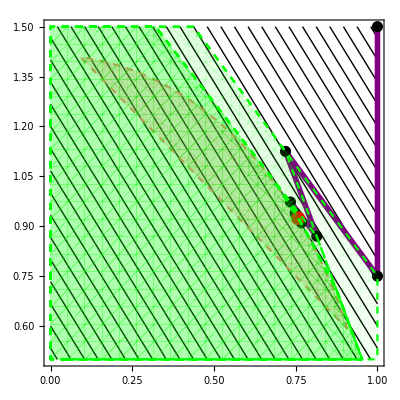

Час роботи методу: 4.9366 s
Нев'язка: 0.0146657
Похибка: 0.000446211
Отримане значення: {0.757068,0.924166}
Значення функції: -21.0161

```mathematica
(*реалізацію методу Келі*)

X={};
CP=Show[
ContourPlot[f[x1,x2],{x1,0,1},{x2,0.5,1.5},ContourShading->None,Contours->{Automatic,50}],RegionPlot[g[x1,x2][[1]]≥ 0&&g[x1,x2][[2]]≥ 0&&g[x1,x2][[3]]≥ 0&&g[x1,x2][[4]]≥ 0&& h[x1,x2][[1]]≥0 &&  h[x1,x2][[2]]≥0 &&   h[x1,x2][[3]]≥0 &&   h[x1,x2][[4]]≥0,{x1,0,1},{x2,0.5,1.5},PlotStyle->{Pink,Opacity[0.2]},BoundaryStyle->{Dashed,Pink}]];
t1=Now;
(*1 ітерація*)
K=h[x1,x2];
Xtemp=NMinimize[{f[x1,x2],K≥0},{x1,x2}][[2,;;,2]];
AppendTo[X,Xtemp];
max=Max[-g[X[[-1,1]], X[[-1,2]]][[1]],-g[X[[-1,1]], X[[-1,2]] ][[2]],-g[X[[-1,1]], X[[-1,2]]][[3]],-g[X[[-1,1]], X[[-1,2]] ][[4]],0];
pos=Position[g[X[[-1,1]], X[[-1,2]]],-max][[1,1]];


array[x1_,x2_]=ToExpression[StringJoin[Riffle[Table[ToString[K[[i]]]<>" >= 0",{i,Length[K]}]," && "]]];
picture=Show[CP,RegionPlot[array[x1,x2],{x1,0,1},{x2,0.5,1.5},PlotStyle->{Green,Opacity[0.3]},BoundaryStyle->{Dashed,Green}]];
tab={{"k","x^(k)","f(x^(k))","ϵ^(k)","K^(p)"},{1,X[[-1]],f[X[[-1,1]],X[[-1,2]]],g[X[[-1,1]],X[[-1,2]]][[pos]],TableForm[K]}};

Do[{
(*  позиціz обмеження, в якому найбільше порушення nа шукаємо нове обмеження за допомогою градіентного методу *)
max=Max[-g[X[[-1,1]], X[[-1,2]]][[1]],-g[X[[-1,1]], X[[-1,2]] ][[2]],-g[X[[-1,1]], X[[-1,2]]][[3]],-g[X[[-1,1]], X[[-1,2]] ][[4]],0];
pos=Position[g[X[[-1,1]], X[[-1,2]]],-max][[1,1]];
grad=Grad[g[x1,x2][[pos]],{x1,x2}]/.Thread[{x1,x2}->X[[-1]]];
linear[x1_,x2_]=Expand[g[X[[-1,1]], X[[-1,2]]][[pos]]+grad.({x1,x2}-X[[-1]])];
AppendTo[K,linear[x1,x2]];
Xtemp=NMinimize[{f[x1,x2],K≥0},{x1,x2}][[2,;;,2]];
AppendTo[X,Xtemp];
array[x1_,x2_]=ToExpression[StringJoin[Riffle[Table[ToString[K[[i]]]<>" >= 0",{i,Length[K]}]," && "]]];
picture=Show[CP,RegionPlot[array[x1,x2],{x1,0,1},{x2,0.5,1.5},PlotStyle->{Green,Opacity[0.5]},BoundaryStyle->{Dashed,Green}]];

AppendTo[tab,{iterator,X[[-1]],f[X[[-1,1]],X[[-1,2]]],g[X[[-1,1]],X[[-1,2]]][[pos]],TableForm[K]}];

If[g[X[[-1,1]],X[[-1,2]]][[pos]]>-ϵ,Break[]]
},{iterator,2,30}];
t2=Now;

point=NMinimize[{f[x1,x2],g[x1,x2][[1]]≥0,g[x1,x2][[2]]≥0,g[x1,x2][[3]]≥ 0,g[x1,x2][[4]]≥ 0},{x1,x2}][[2,;;,2]];

Print["Таблиця результатів:\n"];
Print[Grid[tab,Frame->All,FrameStyle->Gray]];

temp=Table[ToExpression[StringJoin[Riffle[Table[ToString[K[[i]]]<>" >= 0",{i,j}]," && "]]],{j,5,Length[K]}];

Print["Отриманий графік:"];
Print[Show[
CP,
Graphics[{Purple,Thickness[0.01],Line[X],Black,PointSize[0.02],Point[X],Red,PointSize[0.025],Point[X[[-1]]]}],Table[RegionPlot[temp[[k]],{x1,0,1},{x2,0.5,1.5},PlotStyle->{Green,Opacity[0.05]},BoundaryStyle->{Dashed,Green}],{k,1,Length[K]-4}]]];
Print["Час роботи методу: ",t=t2-t1, "\nНев'язка: ",Norm[point-X[[-1]]],"\nПохибка: ",Abs[f[point[[1]],point[[2]]]-f[X[[-1,1]],X[[-1,2]]]],"\nОтримане значення: ",X[[-1]],"\nЗначення функції: ",f[X[[-1,1]],X[[-1,2]]]];


Gr[f_,X0_]:=Grad[f[x1,x2],{x1,x2}]/.Thread[{x1,x2}->X0]
```

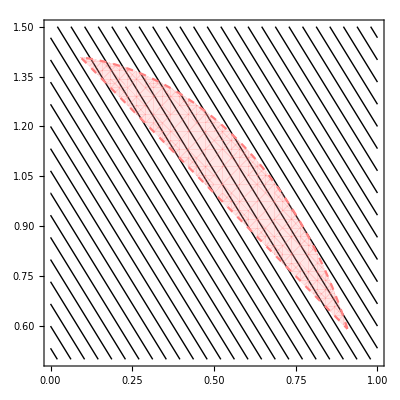

```mathematica
CP=Show[
ContourPlot[f[x1,x2],{x1,0,1},{x2,0.5,1.5},ContourShading->None,Contours->{Automatic,50}],RegionPlot[g[x1,x2][[1]]≥ 0&&g[x1,x2][[2]]≥ 0&&g[x1,x2][[3]]≥ 0&&g[x1,x2][[4]]≥ 0&& h[x1,x2][[1]]≥0 &&  h[x1,x2][[2]]≥0 &&   h[x1,x2][[3]]≥0 &&   h[x1,x2][[4]]≥0,{x1,0,1},{x2,0.5,1.5},PlotStyle->{Pink,Opacity[0.2]},BoundaryStyle->{Dashed,Pink}]]
```